# Les polynômes de Legendre

## Définition du produit scalaire

### Fonction poid

```mathematica
w:=1
```

### Intervalle d’orthogonalité

```mathematica
a:=-1
```

```mathematica
b:=1
```

### Produit scalaire

```mathematica
⟨f_|g_⟩:=∫_a^b w f gⅆx
```

## Norme et normalization

### Norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

## Projection orthogonale

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

## Orthogonalisation (Procédé de Gram-Schmidt)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## Base

### Base orthogonale

```mathematica
dim:=5
```

```mathematica
Subscript[n, min]:=0;Subscript[n, max]:=dim-1;
```

```mathematica
Subscript[𝓊, n_][x_]:=LegendreP[n,x]
```

```mathematica
Table[Subscript[𝓊, n][x],{n,Subscript[n, min],Subscript[n, max]}]//TableForm//TraditionalForm
```

1
x
1/2 (3 x^2-1)
1/2 (5 x^3-3 x)
1/8 (35 x^4-30 x^2+3)

```mathematica
orthogonality[Table[Subscript[𝓊, n][x],{n,Subscript[n, min],Subscript[n, max]}]]
```

2 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0
0 | 0 | 0 | 2/7 | 0
0 | 0 | 0 | 0 | 2/9

### Représentation graphique

```mathematica
Subscript[x, min]:=-1;Subscript[x, max]:=1;
```

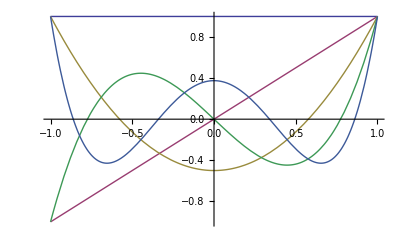

```mathematica
Plot[Evaluate[Table[Subscript[𝓊, n][x],{n,Subscript[n, min],Subscript[n, max]}]],{x,Subscript[x, min],Subscript[x, max]}]
```

### Base orthonormale

On peut normaliser cette base

```mathematica
Subscript[𝓊̃, n_][x_]:=normalize[Subscript[𝓊, n][x]]
```

```mathematica
Table[Subscript[𝓊̃, n][x],{n,Subscript[n, min],Subscript[n, max]}]//Simplify//TableForm//TraditionalForm
```

1/(√2)
√(3/2) x
1/2 √(5/2) (3 x^2-1)
1/2 √(7/2) x (5 x^2-3)
(35 x^4-30 x^2+3)/(√2 √((35 (Integrate`$$a$81722)^4-30 (Integrate`$$a$81722)^2+3)^2))

```mathematica
orthogonality[Table[Subscript[𝓊̃, n][x],{n,Subscript[n, min],Subscript[n, max]}]]
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

### Représentation graphique

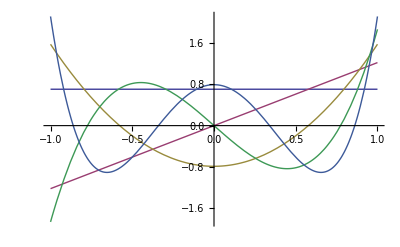

```mathematica
Plot[Evaluate[Table[Subscript[𝓊̃, n][x],{n,Subscript[n, min],Subscript[n, max]}]],{x,Subscript[x, min],Subscript[x, max]}]
```

## Développement

### La fonction à développer

```mathematica
f[x]:=x^6-x^3+x+1
```

### Les coeficients de Fourier

```mathematica
Subscript[a, n_]:=⟨Subscript[𝓊̃, n][x]|f[x] ⟩
```

```mathematica
Table[Subscript[a, n],{n,Subscript[n, min],Subscript[n, max]}]//Simplify
```

{(8 √2)/7,(2 √(2/3))/5,(2 √10)/21,-(2 √(2/7))/5,(8 √2)/77}

### Dévelopement de f(x) sur la base orthonormale

```mathematica
∑_(n=0)^10 Subscript[a, n] Subscript[𝓊̃, n]
```

8/7 √2 (𝓊̃)_0+2/5 √(2/3) (𝓊̃)_1+2/21 √10 (𝓊̃)_2-2/5 √(2/7) (𝓊̃)_3+8/77 √2 (𝓊̃)_4+16/231 √(2/13) (𝓊̃)_6

```mathematica
Manipulate[∑_(n=0)^N Subscript[a, n] Subscript[𝓊̃, n][x],{N,0,10,1}]
```

```mathematica
Manipulate[Plot[Evaluate[{f[x],∑_(n=0)^N Subscript[a, n] Subscript[𝓊̃, n][x]}],{x,Subscript[x, min],Subscript[x, max]},PlotRange->All],{N,0,10,1},ControlType->Setter]
```